# Probabilistic Evaluation

BX Pan
2017.9.28

## Environment Setting

```mathematica
main="/Users/lambda/Documents/Research/3_S2SEvaluation/";
models=Block[{},
	SetDirectory["/Users/lambda/Documents/Research/3_S2SEvaluation/Data"];
	Select[FileNames[],StringFreeQ[#,"."]&]];
```

```mathematica
datasets=Block[{models,primary,size,frequency},
	SetDirectory["/Users/lambda/Documents/Research/3_S2SEvaluation/Data"];
	models=Select[FileNames[],StringFreeQ[#,"."]&];
	primary={
		{Green,"BoM",LinguisticAssistant},    
		{Red,"CMA",LinguisticAssistant},  
		{Purple,"ECCC",LinguisticAssistant}, 
		{Gray,"ECMWF",LinguisticAssistant},
		{Magenta,"HMCR",LinguisticAssistant},   
		{Yellow, "ISAC-CNR",LinguisticAssistant}, 
		{LightPurple,"JMA", LinguisticAssistant},
		{Brown, "KMA",LinguisticAssistant},  
		{Cyan,"Météo-France",LinguisticAssistant},  
		{Blue,"NCEP",LinguisticAssistant},
		{Orange, "UKMO",LinguisticAssistant}};
	size=Map[Block[{data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>".mx"]},
		Dimensions[data[[1]]]][[{1,3}]]&,models];
	frequency=Block[{time,f,e},
		time=Map[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>"_control_time.mx"]&,models];
		f=Map[Round[#[[1]],0.1]&,Map[(DateDifference[#[[1]],#[[-1]]])/(Length[#]+0.0)&,time]];
		e=Map[{#[[1,1]],#[[-1,1]]}&,time];
		Map[If[#[[1]]<1.01,
		"Every day from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]],
		"Every "<>ToString[#[[1]]]<>" days from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]]]&,Transpose[{f,e}]]];
	Map[Flatten,Transpose[{primary,size,frequency}]]];
```

```mathematica
label=TableForm[Map[Flatten[{#[[1]],#[[2]]<>"("<>ToString[#[[3]][[2]]]<>")",#[[4;;]]}]&,datasets],
	TableHeadings->{None,{"","Model","Ensemble Size","Extension(day)","Hincast Frequency"}},
	TableAlignments->Left];
```

```mathematica
SCA=Map[Block[{grid=Import[main<>"Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#≤38.0&)]]]&,models];
NCA=Map[Block[{grid=Import[main<>"Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>38.0,#<=42]&)]]]&,models];
OR=Map[Block[{grid=Import[main<>"Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>42.0,#≤45]&)]]]&,models];
WA=Map[Block[{grid=Import[main<>"Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#>45&)]]]&,models];
```

## Skill Metric

ROC

```mathematica
ClearAll[ROCPoint,ROCScore,ROCDraw]
```

```mathematica
ROCPoint[simu_,obser_,tercile_]:=Block[{point,bisimu,biobser,FalsePositiveRate,TruePositiveRate,result},
		point={Quantile[obser,tercile[[1]]],Quantile[obser,tercile[[2]]]};
		bisimu=Map[If[Between[#,point],1,0]&,simu];
		biobser=Map[If[Between[#,point],1,0]&,obser];
		result=Map[If[And[#[[1]]==1,#[[2]]==0],-1,If[And[#[[1]]==1,#[[2]]==1],1,0]]&,Transpose[{bisimu,biobser}]];
		FalsePositiveRate=(Length[Select[result,#==-1&]]+0.0)/Length[Select[biobser,#==0&]];
		TruePositiveRate=(Length[Select[result,#==1&]]+0.0)/Length[Select[biobser,#==1&]];
		{FalsePositiveRate,TruePositiveRate}]
```

```mathematica
ROCScore[simu_,obser_,interval_:0.08]:=Block[{origin,final,l},
	origin=Table[Prepend[ROCPoint[simu,obser,{tercile,tercile+interval}],tercile+interval/2.0],{tercile,0.0,1-interval,interval}];
	final=Sort[Append[Prepend[origin[[;;,2;;3]],{0,0}],{1,1}],#2[[1]]>#1[[1]]&];
	l=Length[final];
	Total[Abs[(final[[2;;l,1]]-final[[1;;l-1,1]])*(final[[2;;l,2]]+final[[1;;l-1,2]])/2.]]]
```

```mathematica
ROCDraw[simu_,obser_,interval_:0.08]:=Block[{origin,final},
	origin=Table[Prepend[ROCPoint[simu,obser,{tercile,tercile+interval}],tercile+interval/2.0],{tercile,0.0,1-interval,interval}];
	final=Sort[Append[Prepend[origin,{None,0,0}],{None,1,1}],#2[[2]]>#1[[2]]&];
	Labeled[Show[{Plot[x,{x,0,1},PlotStyle->{Dashed,Gray},
				Frame->True,
				GridLines->Automatic,
				ImageSize->250,
				BaseStyle->15,
				PlotRange->{{0,1},{0,1}},
				FrameLabel->{"False Alarm Ratio","Hit Ratio"}],
			ListLinePlot[Map[Labeled[{#[[2]],#[[3]]},#[[1]]]&,final],
				PlotMarkers->Style["*",FontSize->34],PlotRange->{{0,1},{0,1}}]}],
			Style["ROC Score="<>ToString[Round[ROCScore[simu,obser,interval],0.001]],
				FontSize->15],Top]]
```

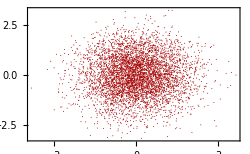
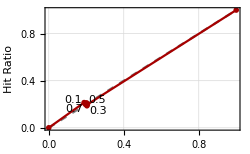
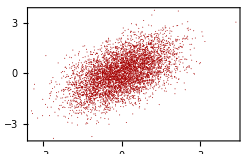
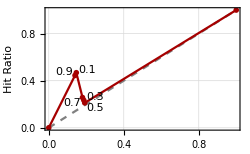
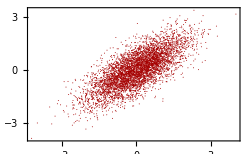
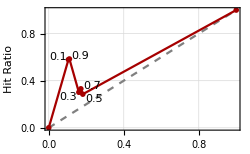
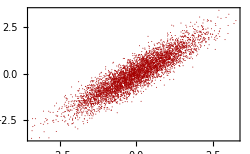
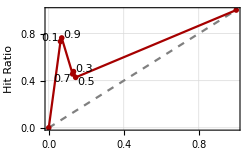
-Graphics-ρ=0. | -Graphics-ROC Score=0.499 | -Graphics-ρ=0.5 | -Graphics-ROC Score=0.539
-Graphics-ρ=0.75 | -Graphics-ROC Score=0.588 | -Graphics-ρ=0.9 | -Graphics-ROC Score=0.682
-Graphics-ρ=0.95 | -Graphics-ROC Score=0.755 | -Graphics-ρ=0.99 | -Graphics-ROC Score=0.878

```mathematica
TableForm[ArrayReshape[Table[{simu,obser}=Transpose[RandomVariate[MultinormalDistribution[{0, 0}, {{1, r}, {r, 1}}],5000]];
{Labeled[ListPlot[Transpose[{simu,obser}],Frame->True,BaseStyle->15,ImageSize->250],Style["ρ="<>ToString[r],FontSize->15],Top],
	ROCDraw[simu,obser,0.2]},{r,{0.,.5,.75,.9,.95,.99}}],{3,4}]]
```

Evaluation

```mathematica
ROCEvaluation[dataset_]:=
Block[{result,
	   SCAsimu,NCAsimu,ORsimu,WAsimu,
	   SCAobser,NCAobser,ORobser,WAobser,
	   mSCAsimu,mNCAsimu,mORsimu,mWAsimu,
	   mSCAobser,mNCAobser,mORobser,mWAobser,
	   iSCAsimu,iSCAobser,iNCAsimu,iNCAobser,
	   imSCAsimu,imNCAsimu,imORsimu,imWAsimu,
	   iORsimu,iORobser,iWAsimu,iWAobser,
	   imSCAobser,imNCAobser,imORobser,imWAobser,
	   GridDaily,GridInterval,RegionalDaily,RegionalInterval,
	   int},
	{{{SCAsimu,NCAsimu,ORsimu,WAsimu},{SCAobser,NCAobser,ORobser,WAobser}},
	 {{iSCAsimu,iNCAsimu,iORsimu,iWAsimu},{iSCAobser,iNCAobser,iORobser,iWAobser}}}=
	 Import[main<>"Data/"<>dataset<>"/"<>dataset<>"_dg.mx"];
	{mSCAsimu,mNCAsimu,mORsimu,mWAsimu}=Map[Flatten[#,1]&,{SCAsimu,NCAsimu,ORsimu,WAsimu}];
	{mSCAobser,mNCAobser,mORobser,mWAobser}=Map[Flatten[Table[#,Dimensions[SCAsimu][[1]]],1]&,{SCAobser,NCAobser,ORobser,WAobser}];
	
	{imSCAsimu,imNCAsimu,imORsimu,imWAsimu}=Map[Map[If[Length[#]==0,0,Flatten[#,1]]&,#]&,{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}];
	{imSCAobser,imNCAobser,imORobser,imWAobser}=Map[Map[If[Length[#]==0,0,Flatten[Table[#,Dimensions[iSCAsimu[[1]]][[1]]],1]]&,#]&,
	{iSCAobser,iNCAobser,iORobser,iWAobser}];
	
GridDaily={ParallelTable[Table[ROCScore[mSCAsimu[[;;,day,grid]],mSCAobser[[;;,day,grid]]],
			{grid,Dimensions[mSCAsimu][[-1]]}],
		    {day,Dimensions[mSCAsimu][[-2]]}],
		   ParallelTable[Table[ROCScore[mNCAsimu[[;;,day,grid]],mNCAobser[[;;,day,grid]]],
			{grid,Dimensions[mNCAsimu][[-1]]}],
		    {day,Dimensions[mNCAsimu][[-2]]}],
		   ParallelTable[Table[ROCScore[mORsimu[[;;,day,grid]],mORobser[[;;,day,grid]]],
			{grid,Dimensions[mORsimu][[-1]]}],
		    {day,Dimensions[mORsimu][[-2]]}],
		   ParallelTable[Table[ROCScore[mWAsimu[[;;,day,grid]],mWAobser[[;;,day,grid]]],
			{grid,Dimensions[mWAsimu][[-1]]}],
		    {day,Dimensions[mWAsimu][[-2]]}]};

RegionalDaily={ParallelTable[ROCScore[Mean[Transpose[Map[Transpose,mSCAsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mSCAobser]]][[;;,day]]],
				{day,Dimensions[mSCAsimu][[2]]}],
			  ParallelTable[ROCScore[Mean[Transpose[Map[Transpose,mNCAsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mNCAobser]]][[;;,day]]],
				{day,Dimensions[mNCAsimu][[2]]}],
              ParallelTable[ROCScore[Mean[Transpose[Map[Transpose,mORsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mORobser]]][[;;,day]]],
	            {day,Dimensions[mORsimu][[2]]}],
              ParallelTable[ROCScore[Mean[Transpose[Map[Transpose,mWAsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mWAobser]]][[;;,day]]],
	            {day,Dimensions[mWAsimu][[2]]}]};
	
GridInterval={ParallelTable[If[Length[imSCAsimu[[i]]]==0,0,
				Table[ROCScore[imSCAsimu[[i]][[;;,grid]],imSCAobser[[i]][[;;,grid]]],
					{grid,Dimensions[imSCAobser[[i]]][[-1]]}]],
			   {i,Length[imSCAobser]}],
			  ParallelTable[If[Length[imNCAsimu[[i]]]==0,0,
				Table[ROCScore[imNCAsimu[[i]][[;;,grid]],imNCAobser[[i]][[;;,grid]]],
					{grid,Dimensions[imNCAobser[[i]]][[-1]]}]],
			   {i,Length[imNCAobser]}],
			  ParallelTable[If[Length[imORsimu[[i]]]==0,0,
				Table[ROCScore[imORsimu[[i]][[;;,grid]],imORobser[[i]][[;;,grid]]],
					{grid,Dimensions[imORobser[[i]]][[-1]]}]],
			   {i,Length[imORobser]}],
			  ParallelTable[If[Length[imWAsimu[[i]]]==0,0,
				Table[ROCScore[imWAsimu[[i]][[;;,grid]],imWAobser[[i]][[;;,grid]]],
					{grid,Dimensions[imWAobser[[i]]][[-1]]}]],
			   {i,Length[imWAobser]}]};

RegionalInterval={ParallelTable[If[Length[imSCAsimu[[i]]]==0,0,
				ROCScore[Mean[Transpose[imSCAsimu[[i]]]],Mean[Transpose[imSCAobser[[i]]]]]],
			   {i,Length[imSCAobser]}],
			  ParallelTable[If[Length[imNCAsimu[[i]]]==0,0,
				ROCScore[Mean[Transpose[imNCAsimu[[i]]]],Mean[Transpose[imNCAobser[[i]]]]]],
			   {i,Length[imNCAobser]}],
			  ParallelTable[If[Length[imORsimu[[i]]]==0,0,
				ROCScore[Mean[Transpose[imORsimu[[i]]]],Mean[Transpose[imORobser[[i]]]]]],
			   {i,Length[imORobser]}],
			  ParallelTable[If[Length[imWAsimu[[i]]]==0,0,
				ROCScore[Mean[Transpose[imWAsimu[[i]]]],Mean[Transpose[imWAobser[[i]]]]]],
			   {i,Length[imWAobser]}]};
			   
result={GridDaily,RegionalDaily,GridInterval,RegionalInterval};
Export["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>dataset<>"_ROC.mx",result]];
```

```mathematica
models
```

{BoM,CMA,ECCC,ECMWF,HCMR,ISACCNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
Map[ROCEvaluation,models]
```

{/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/BoM_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/CMA_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/ECCC_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/ECMWF_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/HCMR_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/ISACCNR_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/JMA_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/KMA_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/MeteoFrance_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/NCEP_ROC.mx,/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/UKMO_ROC.mx}

```mathematica
GridDaily=Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_ROC.mx"];
	Map[Mean[Transpose[#]]&,data[[1]]]]&,models]];
```

```mathematica
RegionalDaily=Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_ROC.mx"];
	data[[2]]]&,models]];
```

```mathematica
GridInterval=Map[Transpose,Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_ROC.mx"];
	Table[Map[If[Length[#]>0,Mean[#],0]&,data[[3,i]]],{i,Dimensions[data][[2]]}]]&,models]]];
```

```mathematica
RegionalInterval=Map[Transpose,Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_ROC.mx"];
	data[[4]]]&,models]]];
```

```mathematica
range={0.48,1};
```

```mathematica
Dimensions[GridDaily]
Dimensions[RegionalDaily]
Dimensions[GridInterval]
Dimensions[RegionalInterval]
```

{4,11}

{4,11}

{4,7,11}

{4,7,11}

```mathematica
GridDailyDraw=Table[ListLinePlot[GridDaily[[region]],
		PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
		PlotRange->range,
		BaseStyle->40,
		Frame->True,
		ImageSize->800,
		FrameLabel->{"Forecast Leading Day","ROC"}],{region,4}];
RegionalDailyDraw=Table[ListLinePlot[RegionalDaily[[region]],
		PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
		PlotRange->range,
		BaseStyle->40,
		Frame->True,
		ImageSize->800,
		FrameLabel->{"Forecast Leading Day","ROC"}],{region,4}];
GridIntervalDraw=Table[BarChart[GridInterval[[region]],
	BaseStyle->40,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange -> {Automatic, range},
    PlotRangePadding -> {Automatic, 0},
    PlotRangeClipping -> True,
	FrameLabel->{"Forecast Interval","ROC"},
	ImageSize->800],{region,4}];
RegionalIntervalDraw=Table[BarChart[RegionalInterval[[region]],
	BaseStyle->40,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange -> {Automatic, range},
    PlotRangePadding -> {Automatic, 0},
    PlotRangeClipping -> True,
	FrameLabel->{"Forecast Interval","ROC"},
	ImageSize->800],{region,4}];
label=Block[{},
	table[pairs_] :=TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig=Labeled[TableForm[Transpose[{GridDailyDraw,RegionalDailyDraw,GridIntervalDraw,RegionalIntervalDraw}],
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
Export["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/fig_ROC.pdf",fig];
```

## LinearROC

ROC

```mathematica
LinearROCScore[simu_,obser_,interval_:0.08]:=Block[{origin,final,l,nsimu,model},
	model=LinearModelFit[Transpose[{simu,obser}],xx,xx];
	nsimu=Map[model,simu];
	origin=Table[Prepend[ROCPoint[nsimu,obser,{tercile,tercile+interval}],tercile+interval/2.0],{tercile,0.0,1-interval,interval}];
	final=Sort[Append[Prepend[origin[[;;,2;;3]],{0,0}],{1,1}],#2[[1]]>#1[[1]]&];
	l=Length[final];
	Total[Abs[(final[[2;;l,1]]-final[[1;;l-1,1]])*(final[[2;;l,2]]+final[[1;;l-1,2]])/2.]]]
```

Evaluation

```mathematica
LinearROCEvaluation[dataset_]:=
Block[{result,
	   SCAsimu,NCAsimu,ORsimu,WAsimu,
	   SCAobser,NCAobser,ORobser,WAobser,
	   mSCAsimu,mNCAsimu,mORsimu,mWAsimu,
	   mSCAobser,mNCAobser,mORobser,mWAobser,
	   iSCAsimu,iSCAobser,iNCAsimu,iNCAobser,
	   imSCAsimu,imNCAsimu,imORsimu,imWAsimu,
	   imSCAobser,imNCAobser,imORobser,imWAobser,
	   iORsimu,iORobser,iWAsimu,iWAobser,
	   GridDaily,GridInterval,RegionalDaily,RegionalInterval,
	   int},
	{{{SCAsimu,NCAsimu,ORsimu,WAsimu},{SCAobser,NCAobser,ORobser,WAobser}},
	 {{iSCAsimu,iNCAsimu,iORsimu,iWAsimu},{iSCAobser,iNCAobser,iORobser,iWAobser}}}=
	 Import[main<>"Data/"<>dataset<>"/"<>dataset<>"_dg.mx"];
	{mSCAsimu,mNCAsimu,mORsimu,mWAsimu}=Map[Flatten[#,1]&,{SCAsimu,NCAsimu,ORsimu,WAsimu}];
	{mSCAobser,mNCAobser,mORobser,mWAobser}=Map[Flatten[Table[#,Dimensions[SCAsimu][[1]]],1]&,{SCAobser,NCAobser,ORobser,WAobser}];
	
	{imSCAsimu,imNCAsimu,imORsimu,imWAsimu}=Map[Map[If[Length[#]==0,0,Flatten[#,1]]&,#]&,{iSCAsimu,iNCAsimu,iORsimu,iWAsimu}];
	{imSCAobser,imNCAobser,imORobser,imWAobser}=Map[Map[If[Length[#]==0,0,Flatten[Table[#,Dimensions[iSCAsimu[[1]]][[1]]],1]]&,#]&,
	{iSCAobser,iNCAobser,iORobser,iWAobser}];
	
GridDaily={ParallelTable[Table[LinearROCScore[mSCAsimu[[;;,day,grid]],mSCAobser[[;;,day,grid]]],
			{grid,Dimensions[mSCAsimu][[-1]]}],
		    {day,Dimensions[mSCAsimu][[-2]]}],
		   ParallelTable[Table[LinearROCScore[mNCAsimu[[;;,day,grid]],mNCAobser[[;;,day,grid]]],
			{grid,Dimensions[mNCAsimu][[-1]]}],
		    {day,Dimensions[mNCAsimu][[-2]]}],
		   ParallelTable[Table[LinearROCScore[mORsimu[[;;,day,grid]],mORobser[[;;,day,grid]]],
			{grid,Dimensions[mORsimu][[-1]]}],
		    {day,Dimensions[mORsimu][[-2]]}],
		   ParallelTable[Table[LinearROCScore[mWAsimu[[;;,day,grid]],mWAobser[[;;,day,grid]]],
			{grid,Dimensions[mWAsimu][[-1]]}],
		    {day,Dimensions[mWAsimu][[-2]]}]};

RegionalDaily={ParallelTable[LinearROCScore[Mean[Transpose[Map[Transpose,mSCAsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mSCAobser]]][[;;,day]]],
				{day,Dimensions[mSCAsimu][[2]]}],
			  ParallelTable[LinearROCScore[Mean[Transpose[Map[Transpose,mNCAsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mNCAobser]]][[;;,day]]],
				{day,Dimensions[mNCAsimu][[2]]}],
              ParallelTable[LinearROCScore[Mean[Transpose[Map[Transpose,mORsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mORobser]]][[;;,day]]],
	            {day,Dimensions[mORsimu][[2]]}],
              ParallelTable[LinearROCScore[Mean[Transpose[Map[Transpose,mWAsimu]]][[;;,day]],
				Mean[Transpose[Map[Transpose,mWAobser]]][[;;,day]]],
	            {day,Dimensions[mWAsimu][[2]]}]};
	
GridInterval={ParallelTable[If[Length[imSCAsimu[[i]]]==0,0,
				Table[LinearROCScore[imSCAsimu[[i]][[;;,grid]],imSCAobser[[i]][[;;,grid]]],
					{grid,Dimensions[imSCAobser[[i]]][[-1]]}]],
			   {i,Length[imSCAobser]}],
			  ParallelTable[If[Length[imNCAsimu[[i]]]==0,0,
				Table[LinearROCScore[imNCAsimu[[i]][[;;,grid]],imNCAobser[[i]][[;;,grid]]],
					{grid,Dimensions[imNCAobser[[i]]][[-1]]}]],
			   {i,Length[imNCAobser]}],
			  ParallelTable[If[Length[imORsimu[[i]]]==0,0,
				Table[LinearROCScore[imORsimu[[i]][[;;,grid]],imORobser[[i]][[;;,grid]]],
					{grid,Dimensions[imORobser[[i]]][[-1]]}]],
			   {i,Length[imORobser]}],
			  ParallelTable[If[Length[imWAsimu[[i]]]==0,0,
				Table[LinearROCScore[imWAsimu[[i]][[;;,grid]],imWAobser[[i]][[;;,grid]]],
					{grid,Dimensions[imWAobser[[i]]][[-1]]}]],
			   {i,Length[imWAobser]}]};

RegionalInterval={ParallelTable[If[Length[imSCAsimu[[i]]]==0,0,
				LinearROCScore[Mean[Transpose[imSCAsimu[[i]]]],Mean[Transpose[imSCAobser[[i]]]]]],
			   {i,Length[imSCAobser]}],
			  ParallelTable[If[Length[imNCAsimu[[i]]]==0,0,
				LinearROCScore[Mean[Transpose[imNCAsimu[[i]]]],Mean[Transpose[imNCAobser[[i]]]]]],
			   {i,Length[imNCAobser]}],
			  ParallelTable[If[Length[imORsimu[[i]]]==0,0,
				LinearROCScore[Mean[Transpose[imORsimu[[i]]]],Mean[Transpose[imORobser[[i]]]]]],
			   {i,Length[imORobser]}],
			  ParallelTable[If[Length[imWAsimu[[i]]]==0,0,
				LinearROCScore[Mean[Transpose[imWAsimu[[i]]]],Mean[Transpose[imWAobser[[i]]]]]],
			   {i,Length[imWAobser]}]};
			   
result={GridDaily,RegionalDaily,GridInterval,RegionalInterval};
Export["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>dataset<>"_LinearROC.mx",result]];
```

```mathematica
models
```

{BoM,CMA,ECCC,ECMWF,HCMR,ISACCNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
LinearROCEvaluation[models[[1]]]
```

$Aborted

```mathematica
LinearROCEvaluation[models[[2]]]
```

```mathematica
LinearROCEvaluation[models[[3]]]
```

```mathematica
LinearROCEvaluation[models[[4]]]
```

```mathematica
LinearROCEvaluation[models[[5]]]
```

```mathematica
LinearROCEvaluation[models[[6]]]
```

```mathematica
LinearROCEvaluation[models[[7]]]
```

```mathematica
LinearROCEvaluation[models[[8]]]
```

```mathematica
LinearROCEvaluation[models[[9]]]
```

```mathematica
LinearROCEvaluation[models[[10]]]
```

```mathematica
LinearROCEvaluation[models[[11]]]
```

```mathematica
GridDaily=Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_LinearROC.mx"];
	Map[Mean[Transpose[#]]&,data[[1]]]]&,models]];
```

```mathematica
RegionalDaily=Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_LinearROC.mx"];
	data[[2]]]&,models]];
```

```mathematica
GridInterval=Map[Transpose,Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_LinearROC.mx"];
	Table[Map[If[Length[#]>0,Mean[#],0]&,data[[3,i]]],{i,Dimensions[data][[2]]}]]&,models]]];
```

```mathematica
RegionalInterval=Map[Transpose,Transpose[Map[Block[{data},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/ROC/"<>#<>"_LinearROC.mx"];
	data[[4]]]&,models]]];
```

```mathematica
range={0.48,1};
```

```mathematica
Dimensions[GridDaily]
Dimensions[RegionalDaily]
Dimensions[GridInterval]
Dimensions[RegionalInterval]
```

{4,11}

{4,11}

{4,7,11}

{4,7,11}

```mathematica
GridDailyDraw=Table[ListLinePlot[GridDaily[[region]],
		PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
		PlotRange->range,
		BaseStyle->40,
		Frame->True,
		ImageSize->800,
		FrameLabel->{"Forecast Leading Day","ROC"}],{region,4}];
RegionalDailyDraw=Table[ListLinePlot[RegionalDaily[[region]],
		PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
		PlotRange->range,
		BaseStyle->40,
		Frame->True,
		ImageSize->800,
		FrameLabel->{"Forecast Leading Day","ROC"}],{region,4}];
GridIntervalDraw=Table[BarChart[GridInterval[[region]],
	BaseStyle->40,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange -> {Automatic, range},
    PlotRangePadding -> {Automatic, 0},
    PlotRangeClipping -> True,
	FrameLabel->{"Forecast Interval","ROC"},
	ImageSize->800],{region,4}];
RegionalIntervalDraw=Table[BarChart[RegionalInterval[[region]],
	BaseStyle->40,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange -> {Automatic, range},
    PlotRangePadding -> {Automatic, 0},
    PlotRangeClipping -> True,
	FrameLabel->{"Forecast Interval","ROC"},
	ImageSize->800],{region,4}];
label=Block[{},
	table[pairs_] :=TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig=Labeled[TableForm[Transpose[{GridDailyDraw,RegionalDailyDraw,GridIntervalDraw,RegionalIntervalDraw}],
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
Export["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/fig_LinearROC.pdf",fig];
```

For a fair comparison across a seamless range of time scales, the verification is performed using data averaged over time windows equal in length to the forecast lead time. At a lead time of one day, skill is greatest in the extratropics around 40-60o latitude, lowest around 20o, and has a secondary local maximum close to the equator. The extratropical skill at this short range is highest in the winter hemisphere presumably due to the higher predictability of winter baroclinic systems.

defining a consistent and useful distance metric on these aspects

The essence of our approach is as follows. We compute the prediction skill at
 a range of lead times, from one day to one month. As the lead time increases, we also
 increase the length of the time window over which the data are averaged for
 verification. This is intended to capture the fact that we are transitioning from
 weather to climate prediction as the lead time increases, and to allow the transition to
 occur smoothly. The skill is computed for both total precipitation and anomalies, and
 comparison is made with the skill achievable by a persistence forecast of the
 precipitation anomalies. For comparison we also evaluate the forecasts at varying lead
time but with a fixed verification window of 1 day.